```mathematica
data = Import["/Users/WillC/montecarloPi/data2.csv"][[;;,;;2]];
```

```mathematica
(*
[#instances, #sec, #cores, #points/instanc]
*)
```

```mathematica
Total[data]/Length[data]
```

{808/3,553.628}

```mathematica
dataavg=Table[Total[data[[i*5+1;;(i+1)*5,;;2]]]/5,{i,0,Floor[Length[data]/5]-1}]
allplot=ListLogLinearPlot[data[[1;;5*Floor[Length[data]/5]]],PlotLegends->{Style["Raw data points",FontSize->12]}];
avgplot=ListLogLinearPlot[dataavg,PlotRange->All,Joined->True,PlotStyle->Red,PlotLegends->{Style["Average",FontSize->12]}];
```

{{1,729.611},{5,503.126},{10,485.517},{100,505.761},{500,521.38},{1000,576.373}}

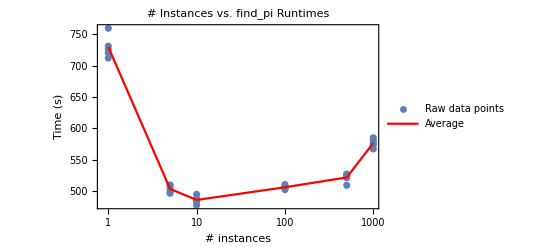

```mathematica
final=Show[{allplot,avgplot},
Frame->True,
FrameLabel->{"# instances","Time (s)"},
LabelStyle->Bold,
PlotLabel->"# Instances vs. find_pi Runtimes"]
```

```mathematica
Rasterize[final,ImageResolution->200]
```

-Graphics-